## Study the sampled parameters

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
transPars=Import["saturationSamplingVaringK.csv"];
pars=Transpose[transPars];
```

```mathematica
us=pars[[Flatten[Position[transPars[[15]],_?(#>0.8&)]]]];
usLow=us[[Flatten[Position[Transpose[us][[19]],_?(0.01<#<0.1&)]]]];
usLowKm2=Flatten[usLow[[RandomInteger[Length[usLow]-1]+1]]];
```

```mathematica
usLowKm2
```

{17.2534,450.934,17.6927,106.865,5.25439,0.148608,0.236667,170.884,86.6245,0.00221059,0.0150061,0.0001,0.1,1,0.818754,0.171653,64003,27.1614,0.0505591,722.045,0.0000255192}

### Now get the dynamics of enzymes in ultrasensitive networks and adaptive network

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1086.9 and t = 1087.21.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1132.73 and t = 1132.84.

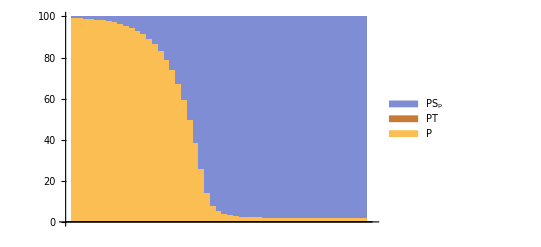

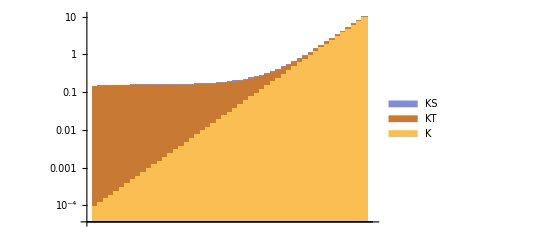

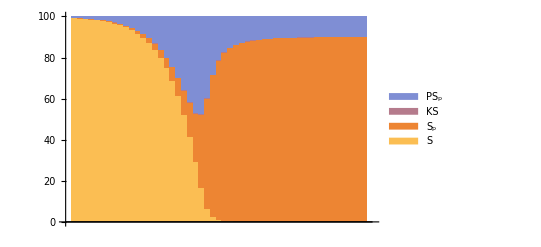

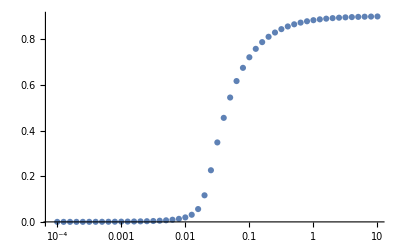

```mathematica
us=pars[[Flatten[Position[transPars[[15]],_?(#>0.8&)]]]];
usLow=us[[Flatten[Position[Transpose[us][[19]],_?(#<0.1&)]]]];
usLowKm2=Flatten[usLow[[RandomInteger[Length[usLow]-1]+1]]];

SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};

vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;

Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,10]==usLowKm2[[Range[10]]]];
Block[{ssthreshold},
totT=usLowKm2[[11]];

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
pt=Evaluate[x[9][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
kt=Evaluate[x[8][ts-0.001]/.sol];
freet=Evaluate[x[7][ts-0.001]/.sol];
s=Evaluate[x[3][ts-0.001]/.sol];
];
];
];
];
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

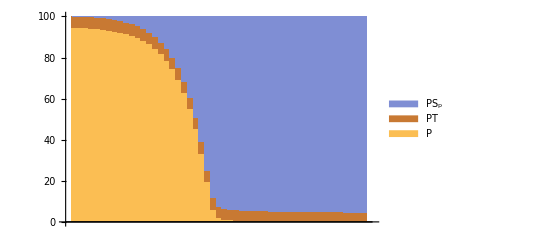

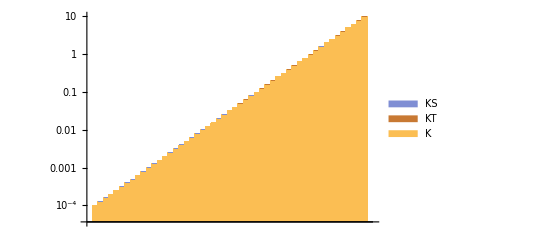

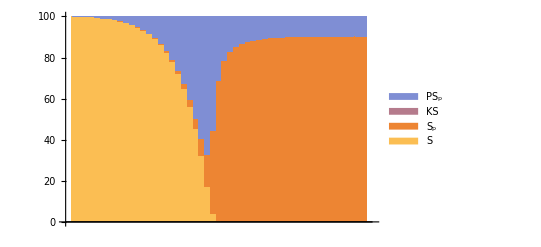

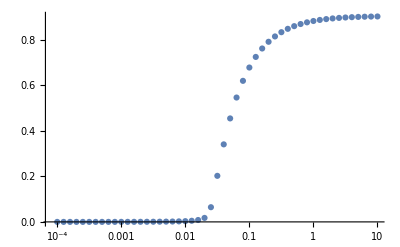

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

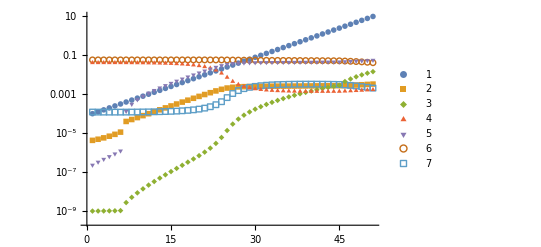

```mathematica
ListLogPlot[{k,ks,kt,p,psp,pt,freet},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

### Now get the dynamics of enzymes in ultrasensitive networks and adaptive network

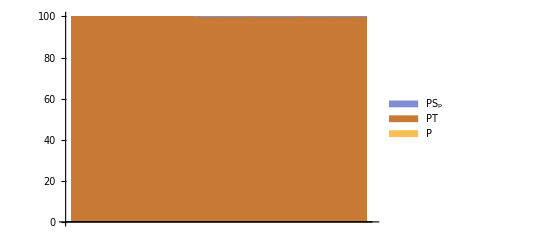

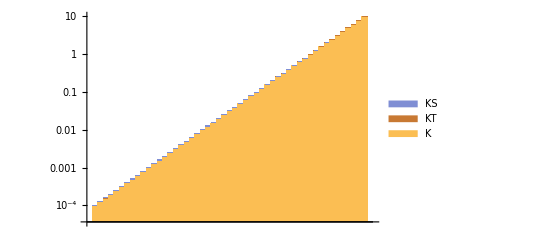

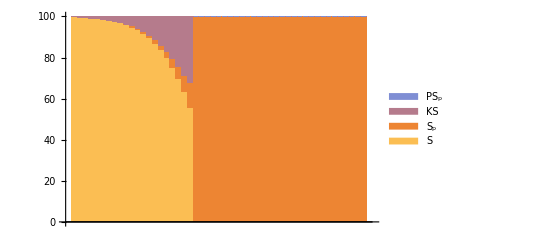

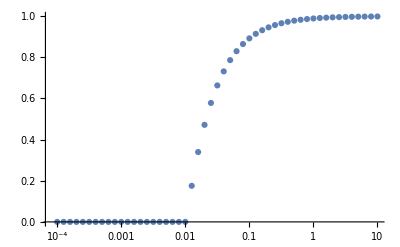

```mathematica
usHigh=us[[Flatten[Position[Transpose[us][[19]],_?(#>10&)]]]];
usHighKm2=Flatten[usHigh[[RandomInteger[Length[usHigh]-1]+1]]];

SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};

vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;

Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,10]==usHighKm2[[Range[10]]]];
Block[{ssthreshold},
totT=usHighKm2[[11]];

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
pt=Evaluate[x[9][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
kt=Evaluate[x[8][ts-0.001]/.sol];
freet=Evaluate[x[7][ts-0.001]/.sol];
s=Evaluate[x[3][ts-0.001]/.sol];
];
];
];
];
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

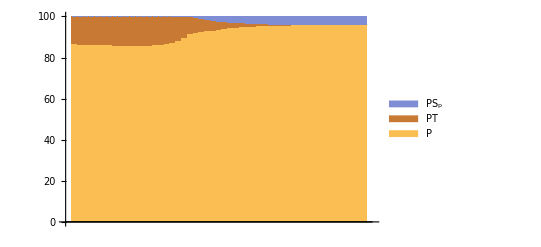

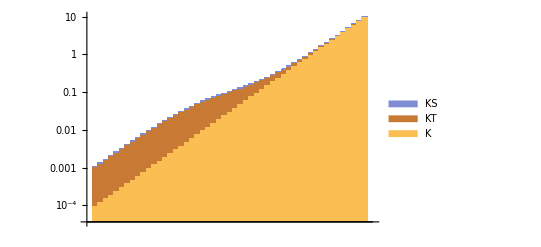

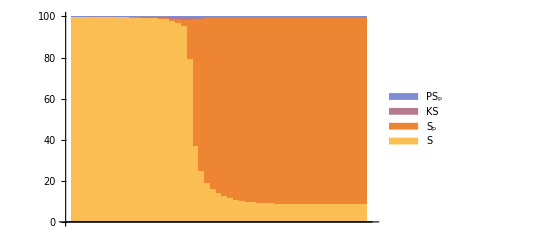

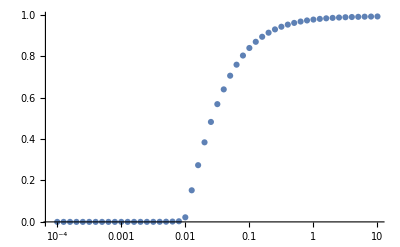

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

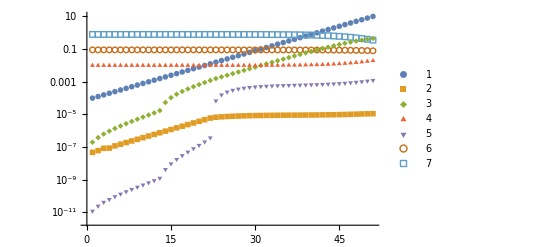

```mathematica
ListLogPlot[{k,ks,kt,p,psp,pt,freet},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```